# Brezposelnost v državah OECD

Podatke pridobimo s spletne strani OECD in jih shranimo v Excelovi tabeli (CSV datoteko moramo z Excelom importati v XLSX). V spodnji tabeli so vsi obstoječi podatki za vse države članice OECD.

```mathematica
podatki=Import["C:\\Users\\katis\\ROM-projekt2\\podatki_OECD_brezposelnost.xlsx"][[1]]
```

{{LOCATION,INDICATOR,SUBJECT,MEASURE,FREQUENCY,TIME,Value},{AUS,HUR,TOT,PC_LF,A,1967.,1.875},{AUS,HUR,TOT,PC_LF,A,1968.,1.85},{AUS,HUR,TOT,PC_LF,A,1969.,1.8},{AUS,HUR,TOT,PC_LF,A,1970.,1.625},{AUS,HUR,TOT,PC_LF,A,1971.,1.925},{AUS,HUR,TOT,PC_LF,A,1972.,2.625},{AUS,HUR,TOT,PC_LF,A,1973.,2.325},65642,{EU27_2020,HUR,WOMEN,PC_LF,M,,8.1},{EU27_2020,HUR,WOMEN,PC_LF,M,,8.3},{EU27_2020,HUR,WOMEN,PC_LF,M,,8.2},{EU27_2020,HUR,WOMEN,PC_LF,M,,8.},{EU27_2020,HUR,WOMEN,PC_LF,M,,7.8},{EU27_2020,HUR,WOMEN,PC_LF,M,,7.7},{EU27_2020,HUR,WOMEN,PC_LF,M,,7.7}}
 |  |  |  |

Seznam vseh članic OECD:

```mathematica
kratice=#[[1]]&/@podatki//Rest//DeleteDuplicates
```

{AUS,AUT,BEL,CAN,CZE,DNK,FIN,FRA,DEU,GRC,HUN,ISL,IRL,ITA,JPN,KOR,LUX,MEX,NLD,NZL,NOR,POL,PRT,SVK,ESP,SWE,CHE,TUR,GBR,USA,CHL,EST,ISR,SVN,EU28,OECD,G-7,EA19,LVA,LTU,COL,EU27_2020}

Slovenska imena:

```mathematica
polnaImena={"Avstralija","Avstrija","Belgija","Kanada","Češka","Danska","Finska","Francija","Nemčija","Grčija","Madžarska","Islandija","Irska","Italija","Japonska","Koreja","Luksemburg","Mehika","Nizozemska","Nova Zelandija", "Norveška", "Poljska", "Portugalska", "Slovaška", "Španija", "Švedska", "CHE","Turčija","V. Britanija", "ZDA","Čile","Estonija","Izrael","Slovenija","EU članice", "OECD članice", "G7 članice", "EA19", "Latvija", "Litva", "Kolumbija", "EU 27-terica"};
```

```mathematica
slovar=Table[polnaImena[[i]]->kratice[[i]],{i,Length[kratice]}]
```

{Avstralija→AUS,Avstrija→AUT,Belgija→BEL,Kanada→CAN,Češka→CZE,Danska→DNK,Finska→FIN,Francija→FRA,Nemčija→DEU,Grčija→GRC,Madžarska→HUN,Islandija→ISL,Irska→IRL,Italija→ITA,Japonska→JPN,Koreja→KOR,Luksemburg→LUX,Mehika→MEX,Nizozemska→NLD,Nova Zelandija→NZL,Norveška→NOR,Poljska→POL,Portugalska→PRT,Slovaška→SVK,Španija→ESP,Švedska→SWE,CHE→CHE,Turčija→TUR,V. Britanija→GBR,ZDA→USA,Čile→CHL,Estonija→EST,Izrael→ISR,Slovenija→SVN,EU članice→EU28,OECD članice→OECD,G7 članice→G-7,EA19→EA19,Latvija→LVA,Litva→LTU,Kolumbija→COL,EU 27-terica→EU27_2020}

Za vsakega od zgornjih podatkov nas zanima le ime članice, “subject” (moški/ženske/vsi), leto in stopnja brezposelnosti.

```mathematica
podatkiOdbrani={#[[1]],#[[3]],#[[6]],#[[7]]}&/@Rest[podatki]
```

{{AUS,TOT,1967.,1.875},{AUS,TOT,1968.,1.85},{AUS,TOT,1969.,1.8},{AUS,TOT,1970.,1.625},{AUS,TOT,1971.,1.925},{AUS,TOT,1972.,2.625},{AUS,TOT,1973.,2.325},{AUS,TOT,1974.,2.7},{AUS,TOT,1975.,4.925},{AUS,TOT,1976.,4.75},{AUS,TOT,1977.,5.65},{AUS,TOT,1978.,6.44253},{AUS,TOT,1979.,6.2655},65630,{EU27_2020,WOMEN,,7.},{EU27_2020,WOMEN,,6.8},{EU27_2020,WOMEN,,6.8},{EU27_2020,WOMEN,,6.8},{EU27_2020,WOMEN,,7.2},{EU27_2020,WOMEN,,7.6},{EU27_2020,WOMEN,,8.1},{EU27_2020,WOMEN,,8.3},{EU27_2020,WOMEN,,8.2},{EU27_2020,WOMEN,,8.},{EU27_2020,WOMEN,,7.8},{EU27_2020,WOMEN,,7.7},{EU27_2020,WOMEN,,7.7}}
 |  |  |  |

Naslednja funkcija bo v odvisnosti od imena države vrnila seznam parov {leto, brezposelnost}. Pri tem vzamemo le subject = “TOT” ter tiste podatke, ki imajo podano tudi leto.

```mathematica
podatkiZaDrzavo[drzava_]:=Module[{sel},sel=Select[podatkiOdbrani,#[[1]]==(drzava/.slovar)&&#[[2]]=="TOT"&&#[[3]]≠""&];Table[{sel[[i]][[3]],sel[[i]][[4]]},{i,Length[sel]}]]
```

```mathematica
podatkiZaDrzavo["Slovenija"]
```

{{1996.,6.89167},{1997.,6.91667},{1998.,7.36667},{1999.,7.40833},{2000.,6.74167},{2001.,6.19167},{2002.,6.34167},{2003.,6.7},{2004.,6.34167},{2005.,6.54167},{2006.,5.99167},{2007.,4.85833},{2008.,4.39167},{2009.,5.89167},{2010.,7.275},{2011.,8.20833},{2012.,8.89167},{2013.,10.1583},{2014.,9.74167},{2015.,9.},{2016.,8.00833},{2017.,6.6},{2018.,5.125},{2019.,4.45},{2020.,4.89167}}

Naslednja funkcija za seznam držav izriše njihove podatke.

```mathematica
Narisi[seznam_]:=ListLinePlot[podatkiZaDrzavo/@seznam,PlotLegends->seznam,ImageSize->Large,PlotLabel->"Stopnja brezposelnosti v držav"<>If[Length[seznam]==1,"i ","ah "]<>StringJoin[Table[If[i==Length[seznam],seznam[[i]],seznam[[i]]<>", "],{i,Length[seznam]}]]]
Narisi[drzava_String]:=Narisi[{drzava}]
```

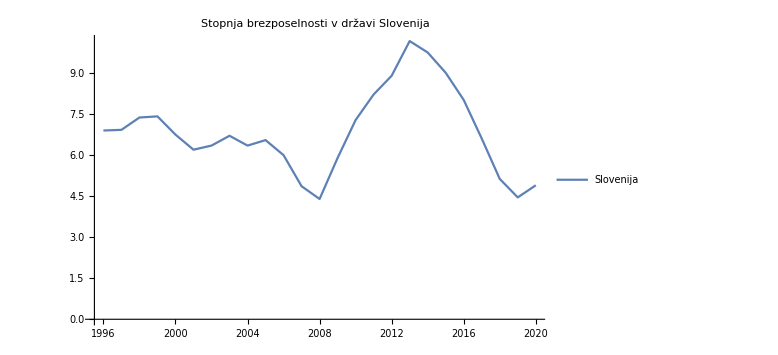

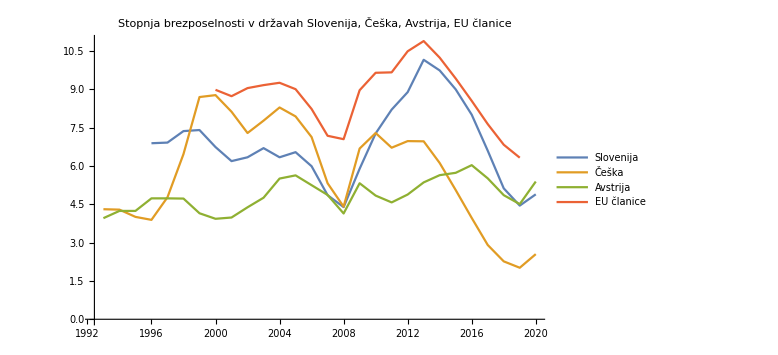

```mathematica
Narisi["Slovenija"]
Narisi[{"Slovenija","Češka","Avstrija","EU članice"}]
```